```mathematica
Clear[travel];
travel[maps_/;0≤maps≤60,stops_,arrival_:{25,0}]:=Module[{base,total,answer},
(*INPUT: maps, travel time as estimated by Google Maps; stops, number of stops on route (e.g., from point A to point B directly: stops = 1); arrival, preferred time of arrival (optional);
OUTPUT: suggested amount of allotted travel time; time of day at which one should leave to arrive at the designated arrival time*)
If[7≤maps≤56,
base=Ceiling[N[10.02*E^(0.043*maps)]],
base=2*maps];
total=base+5*(stops-1);
If[0<total<10,
total=10,
If[total==0,
total = 5]];
If[arrival=={25,0},
answer=total,
answer={total,DatePlus[TimeObject[arrival],{-1*total, "Minute"}]}];
answer]
```

```mathematica
travel[30,1,{12,04}]
```

{37,11:27:00GMT-5.TimeObject[{11,27,0.},TimeZone→-5.]}

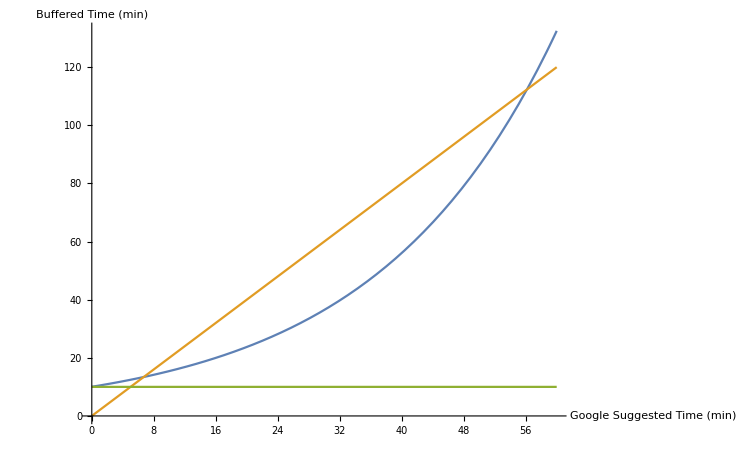

```mathematica
Plot[{10.04*E^(0.043*x),2x,10},{x,0,60},AxesLabel->{"Google Suggested Time (min)", "Buffered Time (min)"},ImageSize->750]
```

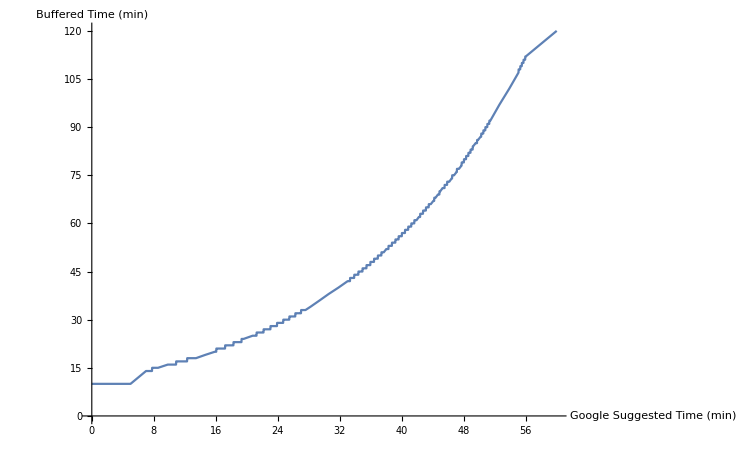

```mathematica
Plot[travel[x,1],{x,0,60},AxesLabel->{"Google Suggested Time (min)", "Buffered Time (min)"},ImageSize->750]
```